```mathematica
i5Single=Import["C:\\Users\\Dejan\\Documents\\single_rez.txt","Table"];
```

```mathematica
gfSingle=Import["C:\\Users\\Dejan\\Documents\\single_gpu_rez.txt","Table"];
```

```mathematica
i5s=Import["C:\\Users\\Dejan\\Documents\\i5_single.txt","Table"];
```

```mathematica
gfs=Import["C:\\Users\\Dejan\\Documents\\gtx_single.txt","Table"];
```

```mathematica
x=Range[35];
```

```mathematica
<<PlotLegends`;
```

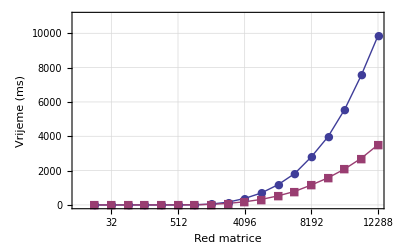

```mathematica
sBrzinaTuring=ListPlot[{i5Single[[All,2]],gfSingle[[All,2]]}, PlotRange->{0,11000},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],gfSingle[[#,1]]}&,Range[2,18,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Vrijeme (ms)"},PlotLegend->{"Intel Core i5-760 (MATLAB - 4 dretve)","Nvidia GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.67,0.28},LegendSize->{1.2,0.3},LegendTextSpace->6]
```

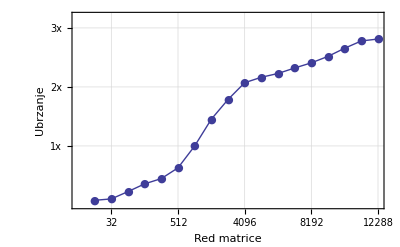

```mathematica
sUbrzanjeTuring=ListPlot[{i5Single[[All,2]]/gfSingle[[All,2]]}, PlotRange->{0,3.2},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small}, FrameTicks->{Map[{x[[#]],gfSingle[[#,1]]}&,Range[2,18,2]],{{1,"1x"},{2,"2x"},{3,"3x"}}},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Ubrzanje"},PlotLegend->{"GeForce GTX 460  -  Core i5-760"},LegendShadow->None,LegendPosition->{-0.8,0.33},LegendSize->{1.1,0.2},LegendTextSpace->6]
```

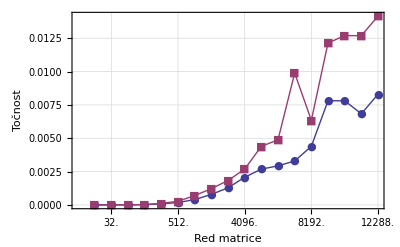

```mathematica
sTocnostTuring=ListPlot[{i5s[[All,4]],i5s[[All,5]]},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],i5Single[[#,1]]}&,Range[2,18,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Točnost"},PlotLegend->{"Intel Core i5-760 (MATLAB)","GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.7,0.3},LegendSize->{0.9,0.25},LegendTextSpace->6]
```

```mathematica
Max[i5s[[All,5]]/i5s[[All,4]]]
```

3.

```mathematica
teslaSingle=Import["C:\\Users\\Dejan\\Documents\\tesla_single.txt","Table"];
```

```mathematica
xeonSingle=Import["C:\\Users\\Dejan\\Documents\\xeon_single.txt","Table"];
```

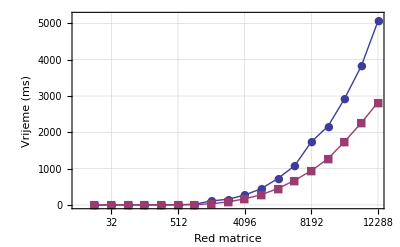

```mathematica
sBrzinaFermi=ListPlot[{xeonSingle[[1;;18,2]],teslaSingle[[1;;18,2]]}, PlotRange->{0,5200},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],gfSingle[[#,1]]}&,Range[2,18,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Vrijeme (ms)"},PlotLegend->{"Intel Xeon E5620 (MATLAB - 8 dretvi)","Nvidia Tesla M2050"},LegendShadow->None,LegendPosition->{-0.67,0.28},LegendSize->{1.2,0.3},LegendTextSpace->6]
```

```mathematica
sUbrzanjeFermi=ListPlot[{xeonSingle[[1;;18,2]]/teslaSingle[[1;;18,2]]}, PlotRange->{0,3.5},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small}, FrameTicks->{Map[{x[[#]],gfSingle[[#,1]]}&,Range[2,18,2]],{{1,"1x"},{2,"2x"},{3,"3x"}}},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Ubrzanje"},PlotLegend->{"Tesla M2050  - Xeon E5620"},LegendShadow->None,LegendPosition->{-0.8,0.33},LegendSize->{1.1,0.2},LegendTextSpace->6]
```

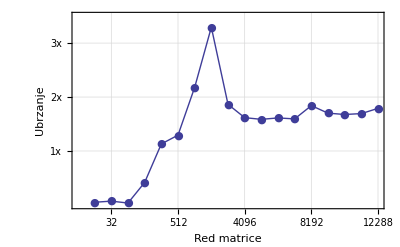

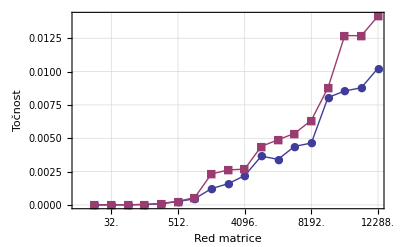

```mathematica
sTocnostFermi=ListPlot[{xeonSingle[[1;;18,4]],xeonSingle[[1;;18,5]]},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],xeonSingle[[#,1]]}&,Range[2,18,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Točnost"},PlotLegend->{"Intel Xeon E5620 (MATLAB)","Nvidia Tesla M2050"},LegendShadow->None,LegendPosition->{-0.7,0.32},LegendSize->{0.9,0.25},LegendTextSpace->6]
```

```mathematica
i5Double=Import["C:\\Users\\Dejan\\Documents\\double_rez.txt","Table"];
```

```mathematica
gfDouble=Import["C:\\Users\\Dejan\\Documents\\double_gpu_rez.txt","Table"];
```

```mathematica
i5d=Import["C:\\Users\\Dejan\\Documents\\i5_double.txt","Table"];
```

```mathematica
gfd=Import["C:\\Users\\Dejan\\Documents\\gtx_double.txt","Table"];
```

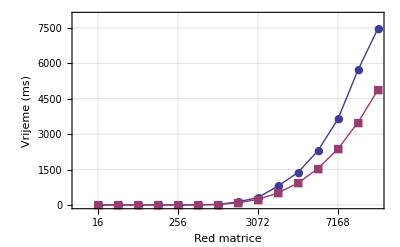

```mathematica
dBrzinaTuring=ListPlot[{i5Double[[All,2]],gfDouble[[All,2]]}, PlotRange->{0,8000},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],gfSingle[[#,1]]}&,Range[1,15,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Vrijeme (ms)"},PlotLegend->{"Intel Core i5-760 (MATLAB - 4 dretve)","Nvidia GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.67,0.28},LegendSize->{1.2,0.3},LegendTextSpace->6]
```

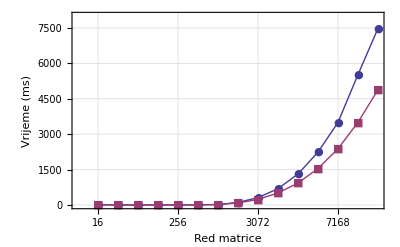

```mathematica
dBrzinaTuring=ListPlot[{i5d[[All,2]],gfd[[All,2]]}, PlotRange->{0,8000},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],gfSingle[[#,1]]}&,Range[1,15,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Vrijeme (ms)"},PlotLegend->{"Intel Core i5-760 (MATLAB - 4 dretve)","Nvidia GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.67,0.28},LegendSize->{1.2,0.3},LegendTextSpace->6]
```

```mathematica
dUbrzanjeTuring=ListPlot[{i5Double[[1;;15,2]]/gfDouble[[1;;15,2]]}, PlotRange->{0,2.2},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small}, FrameTicks->{Map[{x[[#]],gfSingle[[#,1]]}&,Range[1,15,2]],{{1,"1x"},{2,"2x"},{3,"3x"}}},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Ubrzanje"},PlotLegend->{"GeForce GTX 460  -  Core i5-760"},LegendShadow->None,LegendPosition->{-0.8,0.33},LegendSize->{1.1,0.2},LegendTextSpace->6]
```

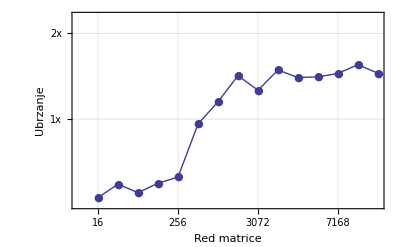

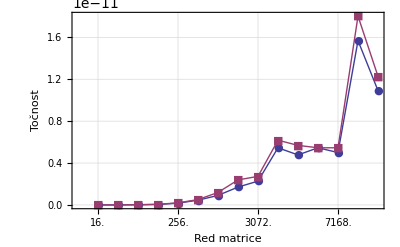

```mathematica
dTocnostTuring=ListPlot[{i5Double[[1;;15,4]],i5Double[[1;;15,5]]},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],i5Double[[#,1]]}&,Range[1,15,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Točnost"},PlotLegend->{"Intel Core i5-760 (MATLAB)","Nvidia GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.5,0.2},LegendSize->{0.9,0.25},LegendTextSpace->6]
```

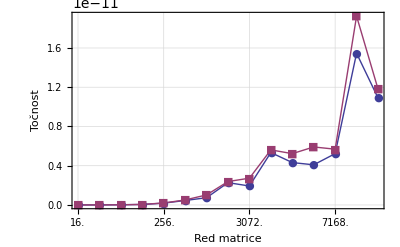

```mathematica
dTocnostTuring=ListPlot[{i5d[[1;;15,4]],i5d[[1;;15,5]]},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],i5Double[[#,1]]}&,Range[1,15,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Točnost"},PlotLegend->{"Intel Core i5-760 (MATLAB)","Nvidia GeForce GTX 460"},LegendShadow->None,LegendPosition->{-0.5,0.2},LegendSize->{0.9,0.25},LegendTextSpace->6,PlotRange->All]
```

```mathematica
teslaDouble=Import["C:\\Users\\Dejan\\Documents\\tesla_double.txt","Table"];
```

```mathematica
xeonDouble=Import["C:\\Users\\Dejan\\Documents\\xeon_double.txt","Table"];
```

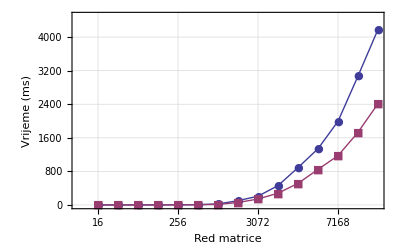

```mathematica
dBrzinaFermi=ListPlot[{xeonDouble[[1;;15,2]],teslaDouble[[1;;15,2]]}, PlotRange->{0,4500},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],gfSingle[[#,1]]}&,Range[1,15,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Vrijeme (ms)"},PlotLegend->{"Intel Xeon E5620 (MATLAB - 8 dretvi)","Nvidia Tesla M2050"},LegendShadow->None,LegendPosition->{-0.67,0.28},LegendSize->{1.2,0.3},LegendTextSpace->6]
```

```mathematica
dUbrzanjeFermi=ListPlot[{xeonDouble[[1;;15,2]]/teslaDouble[[1;;15,2]]}, PlotRange->{0,3.5},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small}, FrameTicks->{Map[{x[[#]],gfSingle[[#,1]]}&,Range[1,15,2]],{{1,"1x"},{2,"2x"},{3,"3x"}}},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Ubrzanje"},PlotLegend->{"Tesla M2050  - Xeon E5620"},LegendShadow->None,LegendPosition->{-0.8,0.33},LegendSize->{1.1,0.2},LegendTextSpace->6]
```

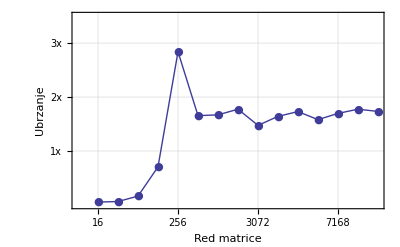

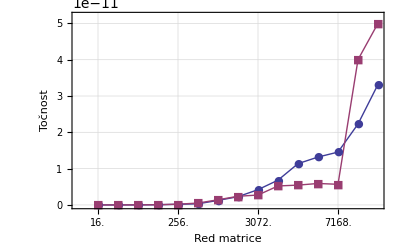

```mathematica
dTocnostFermi=ListPlot[{xeonDouble[[1;;15,4]],xeonDouble[[1;;15,5]]},Joined->True,Mesh->All,GridLines->Automatic,PlotMarkers->{Automatic,Small},FrameTicks->{Map[{x[[#]],xeonSingle[[#,1]]}&,Range[1,15,2]],Automatic},Frame->{{True, False}, {True, False}},FrameLabel->{"Red matrice","Točnost"},PlotLegend->{"Intel Xeon E5620 (MATLAB)","Nvidia Tesla M2050"},LegendShadow->None,LegendPosition->{-0.55,0.28},LegendSize->{0.9,0.25},LegendTextSpace->6,PlotRange->{0, 5.2 10^-11}]
```

```mathematica
Export["C:\\Users\\Dejan\\Documents\\sBrzinaTuring.pdf",sBrzinaTuring]
```

C:\Users\Dejan\Documents\sBrzinaTuring.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\sUbrzanjeTuring.pdf",sUbrzanjeTuring]
```

C:\Users\Dejan\Documents\sUbrzanjeTuring.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\sTocnostTuring.pdf",sTocnostTuring]
```

C:\Users\Dejan\Documents\sTocnostTuring.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\dBrzinaTuring.pdf",dBrzinaTuring]
```

C:\Users\Dejan\Documents\dBrzinaTuring.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\dUbrzanjeTuring.pdf",dUbrzanjeTuring]
```

C:\Users\Dejan\Documents\dUbrzanjeTuring.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\dTocnostTuring.pdf",dTocnostTuring]
```

C:\Users\Dejan\Documents\dTocnostTuring.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\sBrzinaFermi.pdf",sBrzinaFermi]
```

C:\Users\Dejan\Documents\sBrzinaFermi.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\sUbrzanjeFermi.pdf",sUbrzanjeFermi]
```

C:\Users\Dejan\Documents\sUbrzanjeFermi.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\sTocnostFermi.pdf",sTocnostFermi]
```

C:\Users\Dejan\Documents\sTocnostFermi.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\dBrzinaFermi.pdf",dBrzinaFermi]
```

C:\Users\Dejan\Documents\dBrzinaFermi.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\dUbrzanjeFermi.pdf",dUbrzanjeFermi]
```

C:\Users\Dejan\Documents\dUbrzanjeFermi.pdf

```mathematica
Export["C:\\Users\\Dejan\\Documents\\dTocnostFermi.pdf",dTocnostFermi]
```

C:\Users\Dejan\Documents\dTocnostFermi.pdf